## Testing EpidemicKabu with COVID-19 data

In this notebook we count the waves for each country using the data get from EpidemicKabu .

### Getting the data

```mathematica
data=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabuLibrary/examples/data/wavesSizes.csv"];
Length@data
data[[;;10]]//Grid
data[[2;;,1]]//Union
data[[2;;,1]]//Union//Length
```

92

Country | waveNum | max | sum | spanDays | ratioSumSpan
Belgium | 0 | 0.0107959 | 0.527542 | 170 | 0.00310319
Belgium | 1 | 0.0997438 | 5.15165 | 199 | 0.0258877
Belgium | 2 | 0.035368 | 3.62333 | 169 | 0.0214398
Belgium | 3 | 0.132126 | 7.41145 | 173 | 0.0428407
Belgium | 4 | 0.316606 | 14.644 | 87 | 0.168322
Belgium | 5 | 0.0855082 | 4.3808 | 81 | 0.054084
Belgium | 6 | 0.0523065 | 2.93466 | 99 | 0.029643
Belgium | 7 | 0.0153611 | 0.316462 | 21 | 0.0150696
Bosnia and Herzegovina | 0 | 0.0011689 | 0.0534485 | 123 | 0.000434541

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

15

### Counting

```mathematica
totalWavesByC=MapAt[#+1&,GatherBy[data[[2;;]],First][[All,-1]][[All,{1,2}]],{All,2}]
```

{{Belgium,8},{Bosnia and Herzegovina,6},{Brazil,4},{Colombia,5},{Croatia,7},{Ireland,7},{Italy,6},{Luxembourg,8},{Norway,3},{Republic of Korea,4},{Romania,6},{Spain,8},{The United Kingdom,6},{Türkiye,6},{United States of America,7}}

Country with the highest number of waves

```mathematica
MaximalBy[totalWavesByC,Last]
```

{{Belgium,8},{Luxembourg,8},{Spain,8}}

Country with the lowest number of waves

```mathematica
MinimalBy[totalWavesByC,Last]
```

{{Norway,3}}

```mathematica
{{"Brazil",4},{"Norway",4}}
```

{{Brazil,4},{Norway,4}}

Average

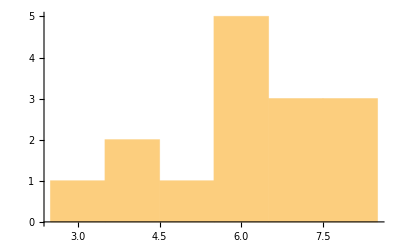
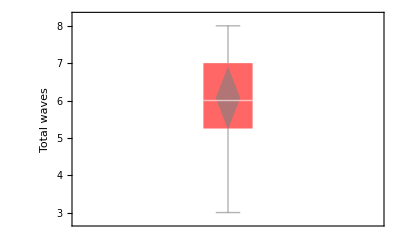
{6.06667,6.,{5.25,6.,7.},1.53375,2.35238,-Graphics-,-Graphics-}

```mathematica
N@{Mean[#],Median[#],Quartiles[#],StandardDeviation[#],Variance[#],Histogram[#],BoxWhiskerChart[#,"Diamond",FrameLabel->{"","Total waves"},ChartStyle->Opacity[0.6,Red]]}&@totalWavesByC[[All,2]]
```